# Solvated Conformers for DrugBank’s Approved Drug Library

## By Madeleine Sutherland

## Introduction

### Purpose

The purpose of this project was to take the organic molecules from Drug Bank’s library of approved drugs, generate diverse conformers for each molecule, and optimize those conformers’ geometries to better reflect the pose(s) the given molecule would adopt in water.  

This project was motivated by a number of recent benchmarking studies such as that by Kanal, et al1 showing that relative energy rankings of molecules’ conformers based on molecular mechanics calculations are inaccurate, but geometry optimization in a semi-empirical framework improves the situation.

#### Example 1: Erythromycin

Here I will show what I did with an example molecule, the antibiotic erythromycin.

First, here’s the SMILES string, as it was curated from the Drug Bank by my collaborator, Janina Kaderli of ETH Zürich.

```mathematica
erySMILES="CC[C@H]([C@](C)([C@@H]([C@@H](C)C([C@H](C)C[C@](C)([C@@H]([C@@H](C)[C@@H]([C@H]1C)O[C@@H](C[C@@]2(C)OC)O[C@@H](C)[C@@H]2O)O[C@@H]([C@@H]2O)O[C@H](C)C[C@@H]2N(C)C)O)=O)O)O)OC1=O"
```

CC[C@H]([C@](C)([C@@H]([C@@H](C)C([C@H](C)C[C@](C)([C@@H]([C@@H](C)[C@@H]([C@H]1C)O[C@@H](C[C@@]2(C)OC)O[C@@H](C)[C@@H]2O)O[C@@H]([C@@H]2O)O[C@H](C)C[C@@H]2N(C)C)O)=O)O)O)OC1=O

```mathematica
eryStartGeo=Molecule[erySMILES]
```

Molecule[…]

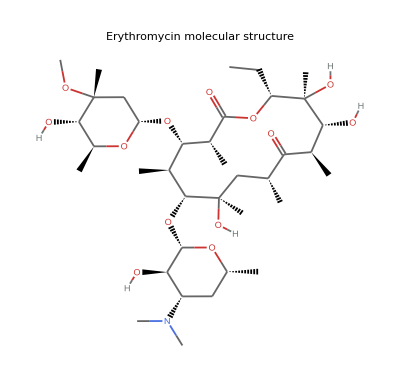

```mathematica
Show[MoleculePlot[eryStartGeo],PlotLabel->HoldForm[Erythromycin molecular structure],LabelStyle->{FontFamily->"Arial",16,GrayLevel[0]}]
```

The next two lines of code define molecular geometries for this demonstration. Conformer driving followed by filtering led to three different conformers, which I then refined by geometry optimization using the PM7 Hamiltonian.

```mathematica
{startconf1,startconf2,startconf3,optconf1,optconf2,optconf3}=
{Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…]}
```

{Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…]}

```mathematica
{startconf2Aligned,startconf3Aligned,optconf2Aligned,optconf3Aligned}={MoleculeAlign[startconf1,startconf2],MoleculeAlign[startconf1,startconf3],MoleculeAlign[optconf1,optconf2],MoleculeAlign[optconf1,optconf3]}
```

{Molecule[…],Molecule[…],Molecule[…],Molecule[…]}

```mathematica
AnnotatedArrow[p_,q_,label_]:={Arrowheads[{{0},{.1,.5,Graphics[Inset[Style[label,Medium],{Left,Top}]]},{.1,1}}],Arrow[{p,q}]}(*Modified from a function in the documentation for Arrow*)
```

Now I will show the whole trajectory from SMILES string to finished project:

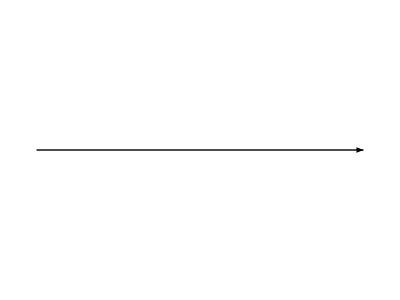
Erythromycin SMILES | -Graphics- | -Graphics3D- | -Graphics- | -Graphics3D- | -Graphics- | -Graphics3D-

```mathematica
Grid[{{
"Erythromycin SMILES",
Graphics[{Arrowheads[.2],AnnotatedArrow[{0,0},{1,0},"Molecule[]"]}],
MoleculePlot3D[eryStartGeo],
Graphics[{Arrowheads[.2],AnnotatedArrow[{0,0},{1,0},"Conformer Driving"]}],
Show[MoleculePlot3D[startconf1,ColorRules->{"C"->Darker[Cyan]}],MoleculePlot3D[startconf2Aligned,ColorRules->{"C"->Yellow}],
MoleculePlot3D[startconf3Aligned,ColorRules->{"C"->Purple}]],
Graphics[{Arrowheads[.2],AnnotatedArrow[{0,0},{1,0},"Geom. Optimization"]}],
Show[MoleculePlot3D[optconf1,ColorRules->{"C"->Darker[Cyan]}],MoleculePlot3D[optconf2Aligned,ColorRules->{"C"->Yellow}],
MoleculePlot3D[optconf3Aligned,ColorRules->{"C"->Purple}]]
}}]
```

Above, the gray molecule is just the 3D geometry of erythromycin as built by Mathematica’s SMILES interpreter. The first set of colorful molecules are the product of molecular mechanics based conformer driving in Open Babel,2 followed by a filtering step run in Python. Conformer driving is a method of rotating all the rotatable bonds in a molecule to simulate the conformers - think of these as the “poses” - available to a molecule. For each molecule in the library, I initially generated 100 conformers, but then I filtered them to remove those that were either unreasonably strained or too similar to the lowest-energy conformer.

The second set of colorful molecules are the conformers’ geometries after optimization in MOPAC3 using the PM7 Hamiltonian and the COSMO solvent model. One beautiful observation is that the three conformers’ geometries appear to have diverged a bit from each other at the end.

#### Example 2: Polymyxin B

Polymyxin B is another antibiotic, in this case a small cyclized peptide. I ended up with nine distinct conformers to optimize.

```mathematica
pmbSMILES="CCC(C)CCCCC(N[C@@H](CCN)C(N[C@@H]([C@@H](C)O)C(N[C@@H](CCN)C(N[C@@H](CCNC([C@H]([C@@H](C)O)NC([C@H](CCN)NC([C@H](CCN)NC([C@H](CC(C)C)NC([C@@H](Cc1ccccc1)NC([C@@H](CCN)N1)=O)=O)=O)=O)=O)=O)C1=O)=O)=O)=O)=O"
```

CCC(C)CCCCC(N[C@@H](CCN)C(N[C@@H]([C@@H](C)O)C(N[C@@H](CCN)C(N[C@@H](CCNC([C@H]([C@@H](C)O)NC([C@H](CCN)NC([C@H](CCN)NC([C@H](CC(C)C)NC([C@@H](Cc1ccccc1)NC([C@@H](CCN)N1)=O)=O)=O)=O)=O)=O)C1=O)=O)=O)=O)=O

```mathematica
pmbStartGeo=Molecule[pmbSMILES]
```

Molecule[…]

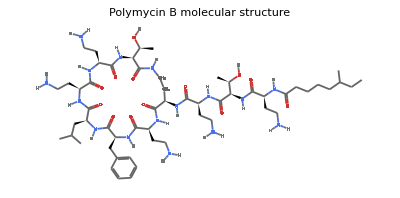

```mathematica
Show[MoleculePlot[pmbStartGeo],PlotLabel->HoldForm[Polymycin B molecular structure],LabelStyle->{FontFamily->"Arial",16,GrayLevel[0]}]
```

First I define and align the conformers of Polymyxin B derived from conformer driving and filtering:

```mathematica
{pmbStartConf1,pmbStartConf2,pmbStartConf3,pmbStartConf4,pmbStartConf5,pmbStartConf6,pmbStartConf7,pmbStartConf8,pmbStartConf9}=
{Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…]};
```

```mathematica
pmbStartAligned=MoleculeAlign[pmbStartConf1,{pmbStartConf2,pmbStartConf3,pmbStartConf4,pmbStartConf5,pmbStartConf6,pmbStartConf7,pmbStartConf8,pmbStartConf9}];
```

```mathematica
pmbStartconfs=Flatten@{pmbStartConf1,pmbStartAligned};
```

Now I will define and align the conformers derived from geometry optimization.

```mathematica
{pmbOptConf1,pmbOptConf2,pmbOptConf3,pmbOptConf4,pmbOptConf5,pmbOptConf6,pmbOptConf7,pmbOptConf8,pmbOptConf9}={Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…],
Molecule[…]};
```

```mathematica
pmbOptAligned=MoleculeAlign[pmbOptConf1,{pmbOptConf2,pmbOptConf3,pmbOptConf4,pmbOptConf5,pmbOptConf6,pmbOptConf7,pmbOptConf8,pmbOptConf9}];
```

```mathematica
pmbOptConfs=Flatten@{pmbOptConf1,pmbOptAligned};
```

```mathematica
colors4mols={RGBColor[0.782803, 0.164904, 0.400458],RGBColor[0.806577, 0.385397, 0.762768],RGBColor[0.698817, 0.873304, 0.295247],RGBColor[0.378897, 0.873304, 0.787549],RGBColor[1, 0.529198, 0.324819],RGBColor[0.723598, 0.791043, 0.963806],RGBColor[1, 0.998856, 0.00207523],RGBColor[1, 0.740871, 0.828473],RGBColor[1, 1, 0.762768]};
```

Now I’ll make the same plot as for erythromycin

```mathematica
Grid[{{
"Polymycin SMILES",
Graphics[{Arrowheads[.2],AnnotatedArrow[{0,0},{1,0},"Molecule[]"]}],
MoleculePlot3D[pmbSMILES],

Graphics[{Arrowheads[.2],AnnotatedArrow[{0,0},{1,0},"Conformer Driving"]}],
Show[
MoleculePlot3D[pmbStartconfs[[1]],ColorRules->{"C"->colors4mols[[1]]}],MoleculePlot3D[pmbStartconfs[[2]],ColorRules->{"C"->colors4mols[[2]]}],
MoleculePlot3D[pmbStartconfs[[3]],ColorRules->{"C"->colors4mols[[3]]}],
MoleculePlot3D[pmbStartconfs[[4]],ColorRules->{"C"->colors4mols[[4]]}],MoleculePlot3D[pmbStartconfs[[5]],ColorRules->{"C"->colors4mols[[5]]}],MoleculePlot3D[pmbStartconfs[[6]],ColorRules->{"C"->colors4mols[[6]]}],MoleculePlot3D[pmbStartconfs[[7]],ColorRules->{"C"->colors4mols[[7]]}],MoleculePlot3D[pmbStartconfs[[8]],ColorRules->{"C"->colors4mols[[8]]}],
MoleculePlot3D[pmbStartconfs[[9]],ColorRules->{"C"->colors4mols[[9]]}]],
Graphics[{Arrowheads[.2],AnnotatedArrow[{0,0},{1,0},"Geom. Optimization"]}],
Show[
MoleculePlot3D[pmbOptConfs[[1]],ColorRules->{"C"->colors4mols[[1]]}],MoleculePlot3D[pmbOptConfs[[2]],ColorRules->{"C"->colors4mols[[2]]}],
MoleculePlot3D[pmbOptConfs[[3]],ColorRules->{"C"->colors4mols[[3]]}],
MoleculePlot3D[pmbOptConfs[[4]],ColorRules->{"C"->colors4mols[[4]]}],MoleculePlot3D[pmbOptConfs[[5]],ColorRules->{"C"->colors4mols[[5]]}],MoleculePlot3D[pmbOptConfs[[6]],ColorRules->{"C"->colors4mols[[6]]}],MoleculePlot3D[pmbOptConfs[[7]],ColorRules->{"C"->colors4mols[[7]]}],MoleculePlot3D[pmbOptConfs[[8]],ColorRules->{"C"->colors4mols[[8]]}],
MoleculePlot3D[pmbOptConfs[[9]],ColorRules->{"C"->colors4mols[[9]]}]]
}}]
```

Polymycin SMILES | -Graphics- | -Graphics3D- | -Graphics- | -Graphics3D- | -Graphics- | -Graphics3D-

```mathematica
AnnotatedArrow2[p_,q_,label_]:={Arrowheads[{{0},{.1,.5,Graphics[Inset[Style[label,Medium],{Right,Top}]]},{.1,1}}],Arrow[{p,q}]}(*Modified from a function in the documentation for Arrow*)
```

It’s easier to visualize the process this molecule went through in a nice vertical panel. Now I will show the nine conformers in a 3x3 grid:

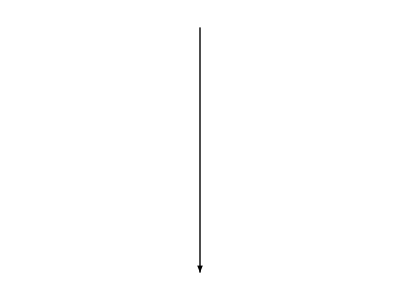
Polymycin SMILES
-Graphics-
-Graphics3D-
-Graphics-
-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics-
-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
Grid[{{
"Polymycin SMILES"},
{Graphics[{Arrowheads[.2],AnnotatedArrow2[{0,0},{0,-1},""]}]},
{MoleculePlot3D[pmbSMILES]},
{Graphics[{Arrowheads[.2],AnnotatedArrow2[{0,0},{0,-1},""]}]},
{Grid[
{{MoleculePlot3D[pmbStartconfs[[1]],ColorRules->{"C"->colors4mols[[1]]}],MoleculePlot3D[pmbStartconfs[[2]],ColorRules->{"C"->colors4mols[[2]]}],
MoleculePlot3D[pmbStartconfs[[3]],ColorRules->{"C"->colors4mols[[3]]}]},
{MoleculePlot3D[pmbStartconfs[[4]],ColorRules->{"C"->colors4mols[[4]]}],MoleculePlot3D[pmbStartconfs[[5]],ColorRules->{"C"->colors4mols[[5]]}],MoleculePlot3D[pmbStartconfs[[6]],ColorRules->{"C"->colors4mols[[6]]}]},{MoleculePlot3D[pmbStartconfs[[7]],ColorRules->{"C"->colors4mols[[7]]}],MoleculePlot3D[pmbStartconfs[[8]],ColorRules->{"C"->colors4mols[[8]]}],
MoleculePlot3D[pmbStartconfs[[9]],ColorRules->{"C"->colors4mols[[9]]}]}}]},
{Graphics[{Arrowheads[.2],AnnotatedArrow2[{0,0},{0,-1},""]}]},
{Grid[
{{MoleculePlot3D[pmbOptConfs[[1]],ColorRules->{"C"->colors4mols[[1]]}],MoleculePlot3D[pmbOptConfs[[2]],ColorRules->{"C"->colors4mols[[2]]}],
MoleculePlot3D[pmbOptConfs[[3]],ColorRules->{"C"->colors4mols[[3]]}]},
{MoleculePlot3D[pmbOptConfs[[4]],ColorRules->{"C"->colors4mols[[4]]}],MoleculePlot3D[pmbOptConfs[[5]],ColorRules->{"C"->colors4mols[[5]]}],MoleculePlot3D[pmbOptConfs[[6]],ColorRules->{"C"->colors4mols[[6]]}]},{MoleculePlot3D[pmbOptConfs[[7]],ColorRules->{"C"->colors4mols[[7]]}],MoleculePlot3D[pmbOptConfs[[8]],ColorRules->{"C"->colors4mols[[8]]}],
MoleculePlot3D[pmbOptConfs[[9]],ColorRules->{"C"->colors4mols[[9]]}]}}]
}}]
```

The result above shows that my workflow succeeded in producing a set of realistic and diverse conformers for this compound.

#### Effect of geometry optimization on Polymyxin B’s conformer geometries

There’s a nice way to visualize the effect of relaxation on a molecule’s conformation. Plot the “old” conformer in grey aligned on top of the “new” conformer in a bright color and see which atoms move.

```mathematica
MoleculeAlign[pmbStartconfs[[1]],pmbOptConfs[[1]]]
```

Molecule[…]

```mathematica
Show[MoleculePlot3D[pmbStartconfs[[1]],ColorRules->{"C"->Gray}],
MoleculePlot3D[MoleculeAlign[pmbStartconfs[[1]],pmbOptConfs[[1]]],ColorRules->{"C"->colors4mols[[1]]}],Background->Black]
```

-Graphics3D-

The plot above shows one conformer before (gray) and after (pink) geometry optimization. Now let’s do the same exercise with all nine conformers, neglecting hydrogens:

```mathematica
Grid[{
{Show[MoleculePlot3D[pmbStartconfs[[1]],ColorRules->{"C"->Gray},PlotTheme->{"HeavyAtom","Tubes"}],
MoleculePlot3D[MoleculeAlign[pmbStartconfs[[1]],pmbOptConfs[[1]]],ColorRules->{"C"->colors4mols[[1]]},PlotTheme->{"HeavyAtom","Tubes"}],Background->Black],
Show[MoleculePlot3D[pmbStartconfs[[2]],ColorRules->{"C"->Gray},PlotTheme->{"HeavyAtom","Tubes"}],
MoleculePlot3D[MoleculeAlign[pmbStartconfs[[2]],pmbOptConfs[[2]]],ColorRules->{"C"->colors4mols[[2]]},PlotTheme->{"HeavyAtom","Tubes"}],Background->Black],
Show[MoleculePlot3D[pmbStartconfs[[3]],ColorRules->{"C"->Gray},PlotTheme->{"HeavyAtom","Tubes"}],
MoleculePlot3D[MoleculeAlign[pmbStartconfs[[3]],pmbOptConfs[[3]]],ColorRules->{"C"->colors4mols[[3]]},PlotTheme->{"HeavyAtom","Tubes"}],Background->Black]},
{Show[MoleculePlot3D[pmbStartconfs[[4]],ColorRules->{"C"->Gray},PlotTheme->{"HeavyAtom","Tubes"}],
MoleculePlot3D[MoleculeAlign[pmbStartconfs[[4]],pmbOptConfs[[4]]],ColorRules->{"C"->colors4mols[[4]]},PlotTheme->{"HeavyAtom","Tubes"}],Background->Black],
Show[MoleculePlot3D[pmbStartconfs[[5]],ColorRules->{"C"->Gray},PlotTheme->{"HeavyAtom","Tubes"}],
MoleculePlot3D[MoleculeAlign[pmbStartconfs[[5]],pmbOptConfs[[5]]],ColorRules->{"C"->colors4mols[[5]]},PlotTheme->{"HeavyAtom","Tubes"}],Background->Black],
Show[MoleculePlot3D[pmbStartconfs[[6]],ColorRules->{"C"->Gray},PlotTheme->{"HeavyAtom","Tubes"}],
MoleculePlot3D[MoleculeAlign[pmbStartconfs[[6]],pmbOptConfs[[6]]],ColorRules->{"C"->colors4mols[[6]]},PlotTheme->{"HeavyAtom","Tubes"}],Background->Black]},
{Show[MoleculePlot3D[pmbStartconfs[[7]],ColorRules->{"C"->Gray},PlotTheme->{"HeavyAtom","Tubes"}],
MoleculePlot3D[MoleculeAlign[pmbStartconfs[[7]],pmbOptConfs[[7]]],ColorRules->{"C"->colors4mols[[7]]},PlotTheme->{"HeavyAtom","Tubes"}],Background->Black],
Show[MoleculePlot3D[pmbStartconfs[[8]],ColorRules->{"C"->Gray},PlotTheme->{"HeavyAtom","Tubes"}],
MoleculePlot3D[MoleculeAlign[pmbStartconfs[[8]],pmbOptConfs[[8]]],ColorRules->{"C"->colors4mols[[8]]},PlotTheme->{"HeavyAtom","Tubes"}],Background->Black],
Show[MoleculePlot3D[pmbStartconfs[[9]],ColorRules->{"C"->Gray},PlotTheme->{"HeavyAtom","Tubes"}],
MoleculePlot3D[MoleculeAlign[pmbStartconfs[[9]],pmbOptConfs[[9]]],ColorRules->{"C"->colors4mols[[9]]},PlotTheme->{"HeavyAtom","Tubes"}],Background->Black]}
}]
```

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-

For all nine conformational states of this Polymyxin B, geometry optimization produced a substantial change. The cyclic backbone of peptide bonds remains more rigid while side chains’ orientations change more dramatically, which fits with what we expect from chemical intuition.

### Methodology Overview

To initiate this procedure, a list of approved drug molecules’ names and SMILES identifiers was generated from the Drug Bank database4. My collaborator at ETH Zürich, Janina Kaderli, ran a round of desalting and duplicate removal and gave me a processed library of molecules to run these calculations on. I used a python script to extract a list of the SMILES identifier strings, and imported them into Mathematica. 

Starting with the list of SMILES strings, a lot of manipulations were needed. Here’s the breakdown of where I performed each of the steps:

```mathematica
Dataset[{
<|"Stage"->"I. Remove molecules I don't want to optimize based on defined criteria","Platform"->"Mathematica"|>,
<|"Stage"->"II. Generate 3D starting geometries","Platform"->"Mostly Mathematica"|>,
<|"Stage"->"III. Run conformer driving and filtering","Platform"->"Python; Open Babel"|>,
<|"Stage"->"IV. Geometry optimize all the conformers","Platform"->"MOPAC"|>,
<|"Stage"->"V. Diagnose failed jobs","Platform"->"Mathematica"|>,
<|"Stage"->"VI. Extract final conformers, visualize","Platform"->"Mathematica"|>},DatasetTheme->"Web"
]
```

## Project Stages in More Detail

### I. Removing molecules I don’t want to optimize

Here’s a subset of 50 molecules I can demonstrate with:

```mathematica
smiles2Dem={"CC[C@H](C)[C@@H](C(N(CCC1)[C@@H]1C(N[C@@H](CCC(O)=O)C(N[C@@H](CCC(O)=O)C(N[C@@H](Cc(cc1)ccc1O)C(N[C@@H](CC(C)C)C(O)=O)=O)=O)=O)=O)=O)NC([C@H](CCC(O)=O)NC([C@H](CCC(O)=O)NC([C@H](Cc1ccccc1)NC([C@H](CC(O)=O)NC(CNC([C@H](CC(N)=O)NC(CNC(CNC(CNC(CNC([C@H](CCC1)N1C([C@H](CCCNC(N)=N)NC([C@H](CCC1)N1C([C@@H](Cc1ccccc1)N)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O","CCNC([C@H](CCC1)N1C([C@H](CCCNC(N)=N)NC([C@H](CC(C)C)NC([C@@H](CC(C)C)NC([C@H](Cc(cc1)ccc1O)NC([C@H](CO)NC([C@H](Cc1c[nH]c2c1cccc2)NC([C@H](Cc1c[nH]cn1)NC([C@H](CC1)NC1=O)=O)=O)=O)=O)=O)=O)=O)=O)=O","CC(C)C[C@@H](C(N[C@@H](CCCN=C(N)N)C(N(CCC1)[C@@H]1C(NNC(N)=O)=O)=O)=O)NC([C@@H](COC(C)(C)C)NC([C@H](Cc(cc1)ccc1O)NC([C@H](CO)NC([C@H](Cc1c[nH]c2c1cccc2)NC([C@H](Cc1cnc[nH]1)NC([C@H](CC1)NC1=O)=O)=O)=O)=O)=O)=O","CC(C)C[C@H](C(N[C@@H](C)C(N[C@H](C(C)C)C(N[C@@H](C(C)C)C(N[C@H](C(C)C)C(N[C@@H](Cc1c[nH]c2c1cccc2)C(N[C@H](CC(C)C)C(N[C@@H](Cc1c[nH]c2c1cccc2)C(N[C@H](CC(C)C)C(N[C@@H](Cc1c[nH]c2c1cccc2)C(N[C@H](CC(C)C)C(N[C@@H](Cc1c[nH]c2c1cccc2)C(NCCO)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)NC(CNC([C@H](C(C)C)NC=O)=O)=O","NC(CC[C@@H](C(N[C@@H](CC(N)=O)C(N[C@@H](CSSCCC(N[C@@H](Cc(cc1)ccc1O)C(N[C@H]1Cc2ccccc2)=O)=O)C(N(CCC2)[C@@H]2C(N[C@H](CCCNC(N)=N)C(NCC(N)=O)=O)=O)=O)=O)=O)NC1=O)=O","CC(C)C[C@@H](C(N[C@@H](CCCNC(N)=N)C(N(CCC1)[C@@H]1C(N[C@H](C)C(N)=O)=O)=O)=O)NC([C@@H](CCCNC(N)=O)NC([C@H](Cc(cc1)ccc1O)NC([C@H](CO)NC([C@@H](Cc1cnccc1)NC([C@@H](Cc(cc1)ccc1Cl)NC([C@@H](Cc1cc2ccccc2cc1)NC(C)=O)=O)=O)=O)=O)=O)=O","NC(CSSCC(C(N(CCC1)C1C(NC(CCCN=C(N)N)C(NCC(N)=O)=O)=O)=O)NC(C(CC(N)=O)NC(C(CCC(N)=O)NC(C(Cc1ccccc1)NC(C(Cc(cc1)ccc1O)N1)=O)=O)=O)=O)C1=O","NCCCCC(C(NCC(N)=O)=O)NC(C(CCC1)N1C(C(CSSCC(C(NC(Cc(cc1)ccc1O)C(NC(Cc1ccccc1)C(NC(CCC(N)=O)C(NC1CC(N)=O)=O)=O)=O)=O)N)NC1=O)=O)=O","CCCCCCCCCC(N[C@@H](Cc1c[nH]c2c1cccc2)C(N[C@H](CC(N)=O)C(N[C@@H](CC(O)=O)C(N[C@@H]([C@@H](C)OC([C@H](CC(c(cccc1)c1N)=O)NC([C@H]([C@H](C)CC(O)=O)NC([C@@H](CO)NC(CNC([C@H](CC(O)=O)NC([C@@H](C)NC([C@H](CC(O)=O)NC([C@H](CCCN)NC(CN1)=O)=O)=O)=O)=O)=O)=O)=O)=O)C1=O)=O)=O)=O)=O","CC[C@@H](C(N(C)CC(N(C)[C@@H](CC(C)C)C(N[C@@H](C(C)C)C(N(C)[C@@H](CC(C)C)C(N[C@@H](C)C(N[C@H](C)C(N(C)[C@@H](CC(C)C)C(N(C)[C@@H](CC(C)C)C(N(C)[C@@H](C(C)C)C(N(C)[C@H]1[C@@H]([C@H](C)C/C=C/C)O)=O)=O)=O)=O)=O)=O)=O)=O)=O)=O)NC1=O","C[C@H]([C@@H](CO)NC([C@H](CSSC[C@@H](C(N[C@@H](Cc1ccccc1)C(N[C@H](Cc1c[nH]c2c1cccc2)C(N[C@@H](CCCCN)C(N[C@H]1[C@@H](C)O)=O)=O)=O)=O)NC([C@@H](Cc2ccccc2)N)=O)NC1=O)=O)O","CC(C)C[C@@H](C(N[C@@H](CCCCNC(C)C)C(N(CCC1)[C@@H]1C(N[C@H](C)C(N)=O)=O)=O)=O)NC([C@@H](CC(N)=O)NC([C@H](Cc(cc1)ccc1O)N(C)C([C@H](CO)NC([C@@H](Cc1cnccc1)NC([C@@H](Cc(cc1)ccc1Cl)NC([C@@H](Cc1cc2ccccc2cc1)NC(C)=O)=O)=O)=O)=O)=O)=O","C[C@H](CNC(CC[C@](C)([C@H]1CC(N)=O)C(/C(/C)=C(/[C@@H](CCC(N)=O)C2(C)C)\\N=C2/C=C(/[C@@H](CCC(N)=O)[C@]2(C)CC(N)=O)\\N=C2/C(/C)=C2/[C@@H](CCC(N)=O)[C@]3(C)CC(N)=O)=N[C@H]1[C@]3(C)N2[Co+]C#N)=O)OP([O-])(O[C@H]([C@@H](CO)O[C@@H]1n2c(cc(C)c(C)c3)c3nc2)[C@H]1O)=O","CC(C)(C)OC(NCCC(N[C@@H](Cc1c[nH]c2c1cccc2)C(N[C@@H](CCSC)C(N[C@@H](CC(O)=O)C(N[C@@H](Cc1ccccc1)C(N)=O)=O)=O)=O)=O)=O","CC(C)C[C@@H](B(O)O)NC([C@H](Cc1ccccc1)NC(c1nccnc1)=O)=O","CC[C@H]([C@](C)([C@@H]([C@@H](C)C([C@H](C)C[C@](C)([C@@H]([C@@H](C)[C@@H]([C@H]1C)O[C@@H](C[C@@]2(C)OC)O[C@@H](C)[C@@H]2O)O[C@@H]([C@@H]2O)O[C@H](C)C[C@@H]2N(C)C)O)=O)O)O)OC1=O","C[C@H](CNC(CC[C@](C)([C@@H](CC(N)=O)[C@H]([C@@](C)([C@@](C)(CC(N)=O)[C@@H]1CCC(N)=O)[N+]2=C1C(C)=C([C@@](C)(CC(N)=O)[C@@H]1CCC(N)=O)[N+]3=C1C=C1C(C)(C)[C@@H]4CCC(N)=O)N56)C6=C(C)C4=[N+]1[Co-3]235([n+]1cn([C@H]([C@@H]2O)O[C@H](CO)[C@H]2O2)c3c1cc(C)c(C)c3)O)=O)OP2([O-])=O","CC[C@@H]([C@@](C)([C@H]([C@H](C)N(C)C[C@@H](C)C[C@@](C)([C@H]([C@H](C)[C@H]([C@@H]1C)O[C@H](C[C@]2(C)OC)O[C@H](C)[C@H]2O)O[C@H]([C@H]2O)O[C@@H](C)C[C@H]2N(C)C)O)O)O)OC1=O","OC(C(O[C@@H]1C[C@H](CC2)[N+]3(CCCC3)[C@H]2C1)=O)(c1ccccc1)c1ccccc1","CCC1=C(C)CN(C(NCCc(cc2)ccc2S(NC(N[C@H]2CC[C@H](C)CC2)=O)(=O)=O)=O)C1=O","CNC(CN1(CCN2(CCN3(C4)CC([O-]5)=O)CC([O-]6)=O)CC([O-]7)=O)=O[Gd+3]123567O=C4NC","CN([C@H](CC1)C2)[C@@H]1C[C@H]2OC(c1ccccc1)c1ccccc1","C[C@@H]([C@H]([C@H]([C@H]([C@H](C(O)=C(C(N)=O)C1=O)N(C)C)[C@@]11O)O)C2=C1O)c1cccc(O)c1C2=O","C[C@@]([C@H](C[C@H]([C@H](C(O)=C(C(NCNCCCC[C@H](C(O)=O)N)=O)C1=O)N(C)C)[C@@]11O)C2=C1O)(c1cccc(O)c1C2=O)O","C[C@H]([C@H]([C@H](C)NC([C@@H]([C@@H](c1c[nH]cn1)OC(C(C1O)OC(C(C2OC(N)=O)O)OC(CO)C2O)OC(CO)C1O)NC(c1nc([C@@H](CC(N)=O)NC[C@H](C(N)=O)N)nc(N)c1C)=O)=O)O)C(N[C@H]([C@H](C)O)C(NCCc1nc(-c2nc(C(NCCC[S+](C)C)=O)cs2)cs1)=O)=O","CC(C)OC(OCOP(CO[C@H](C)Cn1c2ncnc(N)c2nc1)(OCOC(OC(C)C)=O)=O)=O","NC[C@H](CC1)CC[C@@H]1C(O)=O","CC[C@@](C[C@@H](C1)C[C@@]2(C(OC)=O)c(cc([C@@](CC3)([C@@H]4N3CC=C[C@]4(CC)[C@@H]([C@]3(C(N)=O)O)O)[C@@H]3N3C)c3c3)c3OC)(CN1CCc1c2[nH]c2c1cccc2)O","NCCC[C@@H](CC(NC[C@@H](C(N/C(/C(N[C@@H]([C@@H]1NC(N)=NCC1)C(NC[C@@H](C(N[C@H]1CO)=O)N)=O)=O)=C/NC(N)=O)=O)NC1=O)=O)N","C[C@@H](C(N[C@@H](CNC(C[C@H](CCCN)N)=O)C(N/C(/C(N[C@@H]([C@@H]1NC(N)=NCC1)C(NC[C@@H]1N)=O)=O)=C/NC(N)=O)=O)=O)NC1=O","N#C[Fe-2](C#N)(C#N)(C#N)(C#N)N=O","[O-]C(C([C@H]([C@@H]([C@H]([C@H](CO)O)O)O)O)O)=O","CC(C)[N+](C)([C@H](CC1)C2)[C@@H]1C[C@H]2OC(C(CO)c1ccccc1)=O","Cc1cc(C(N2CCN(C)CC2)=Nc(cccc2)c2N2)c2s1","CC[C@@H](/C=C(\\C)/C[C@@H](C)C[C@H]([C@@H]([C@@H](C[C@@H]1C)OC)O[C@@]1(C(C(N(CCCC1)[C@H]1C(O[C@H]([C@@H](C)[C@@H](C1)O)/C(/C)=C/[C@@H](CC[C@H]2Cl)C[C@@H]2OC)=O)=O)=O)O)OC)C1=O","Nc1cc(N2CCCCC2)nc(N)[n+]1[O-]","CC[C@]1([C@@H]([C@]([C@H]2N(C)c3c4)(C(OC)=O)O)OC(C)=O)C=CCN(CC5)[C@H]1[C@]25c3cc([C@@](C[C@H](C1)C=C(CC)CN1C1)(C(OC)=O)c2c1c(cccc1)c1[nH]2)c4OC","CCCCCOc(cc1)ccc1-c(cc1)ccc1-c(cc1)ccc1C(N[C@H](C[C@@H]([C@@H](NC([C@@H]([C@@H]([C@H](C)C1)O)N1C([C@@H]([C@H](C)O)NC([C@@H]([C@H]([C@@H](c(cc1)ccc1O)O)O)NC([C@@H](C[C@@H](C1)O)N1C([C@@H]([C@H](C)O)N1)=O)=O)=O)=O)=O)O)O)C1=O)=O","CN(CC1)CCN1C1=Nc(cc(cc2)Cl)c2Nc2c1cccc2","O[Al](O)OS(OC[C@@H]([C@@H]([C@H]1OS(O[Al](O)O)(=O)=O)OS(O[Al](O)O)(=O)=O)O[C@]1(COS(O[Al](O)O)(=O)=O)O[C@@H]([C@H]([C@@H]1OS(O[Al](O)O)(=O)=O)OS(O[Al](O)O)(=O)=O)O[C@@H](COS(O[Al](O)O)(=O)=O)[C@@H]1OS(O[Al](O)O)(=O)=O)(=O)=O","O[Al](O)O","CCCCC(OCC([C@](C[C@H](c1c(c(C(c(c2ccc3)c3OC)=O)c3C2=O)O)O[C@H](C[C@H]2NC(C(F)(F)F)=O)O[C@H](C)[C@@H]2O)(Cc1c3O)O)=O)=O","C[C@H]([C@H]([C@H](C1)O)O)O[C@H]1O[C@H]([C@@H](C)O[C@H](C1)O[C@H]([C@@H](C)O[C@H](C2)O[C@@H](CC3)C[C@@H](CC4)[C@@]3(C)[C@@H](C[C@H]([C@]3(C)[C@H](CC5)C(CO6)=CC6=O)O)[C@@H]4[C@]35O)[C@H]2O)[C@H]1O","C[C@H]([C@@H](C(NCC(N[C@@H](Cc1c[nH]c2c1cccc2)C(N[C@@H](CCSC)C(N[C@@H](CC(O)=O)C(N[C@@H](Cc1ccccc1)C(N)=O)=O)=O)=O)=O)=O)NC([C@H](Cc(cc1)ccc1OS(O)(=O)=O)NC([C@H](CC(O)=O)NC([C@H](CCC(N)=O)NC([C@H](CC1)NC1=O)=O)=O)=O)=O)O","C[C@@H]([C@H](C)O)[C@@H]1O[C@H]1C[C@@H](CO[C@@H](C/C(/C)=C/C(OCCCCCCCCC(O)=O)=O)[C@@H]1O)[C@H]1O","CN([C@H](CC1)C2)[C@@H]1C[C@H]2OC([C@H](CO)c1ccccc1)=O","CCCCC[C@@](C)(/C=C/[C@H]([C@@H](C/C=C\\CCCC(O)=O)[C@H](C1)O)[C@H]1O)O","Cl[C@H]([C@H]([C@@H]([C@@H]([C@H]1Cl)Cl)Cl)Cl)[C@H]1Cl","N=O","C[C@@]([C@@H]1C(OC)=O)(C(C(/C=C(/C(C)=C2C=C)\\N/C2=C\\C(C(C)=C2CCC(O)=O)=N/C2=C2)=N3)=CC=C1C(OC)=O)/C3=C/c1c(C)c(CCC(OC)=O)c2[nH]1"};
```

I need to extract lists of atomic numbers from these SMILES strings:

```mathematica
atomListExtractor[string_]:=AtomList[Molecule[string],Atom[_],"AtomicNumber"]
```

```mathematica
SetAttributes[atomListExtractor,Listable]
```

```mathematica
atomLists=atomListExtractor[smiles2Dem];
```

Molecule::valenc: Invalid valence for nitrogen atom at position 5.

The three classes of compounds I don’t wish to simulate right now are:

Fewer than 3 heavy atoms (because for such compounds, my conformer generation and refinement process is a phantasmagorical waste of time)

Inorganic

Containing a transition or post-transition metal.

For the third criterion, I define a list of atomic numbers I wish to exclude:

```mathematica
tmLAPostTMNums=Flatten@{13,Range[21,31],Range[39,50],Range[57,84],Range[89,108]}
```

{13,21,22,23,24,25,26,27,28,29,30,31,39,40,41,42,43,44,45,46,47,48,49,50,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108}

The next function will sort away those compounds.

```mathematica
moleculesorter[list_]:=If[Length[DeleteCases[list,1]]<3||ContainsAny[list,tmLAPostTMNums]||ContainsNone[list,{6}],no,yes]
```

```mathematica
yesAndNoDem=Map[moleculesorter,atomLists,{-2}]
```

{yes,yes,yes,yes,yes,yes,yes,yes,yes,yes,yes,yes,no,yes,yes,yes,no,yes,yes,yes,no,yes,yes,yes,yes,yes,yes,yes,yes,yes,no,yes,yes,yes,yes,yes,yes,yes,yes,no,no,yes,yes,yes,yes,yes,yes,yes,no,yes}

Now I will put the compounds I actually want to work with into a new list:

```mathematica
yesIndices=Flatten@Position[yesAndNoDem,yes]
```

{1,2,3,4,5,6,7,8,9,10,11,12,14,15,16,18,19,20,22,23,24,25,26,27,28,29,30,32,33,34,35,36,37,38,39,42,43,44,45,46,47,48,50}

```mathematica
Length[yesIndices]
```

43

```mathematica
compoundsToSimulate=smiles2Dem[[yesIndices]];
```

```mathematica
Length[compoundsToSimulate]
```

43

### II. Generating starting geometries

From there, generating starting geometries was pretty much just converting SMILES Molecule objects and exporting the geometries in a format I could use such as .xyz or, more advisably, .sdf. Example code for this step:

```mathematica
smilesToXYZtest2[n_]:=Export[StringJoin["<desired directory>"<>ToString[yesIndices[[n]]]<>".xyz"],MoleculeModify[Molecule[compoundsToSimulate[[n]]],"AddHydrogens"]]
```

```mathematica
SetAttributes[smilesToXYZtest2,Listable]
```

I later discovered a bug in Mathematica wherein the .xyz file exporter wasn’t writing atomic charges, so the molecules with charged atoms ended up with incorrect bonding structures. I submitted a bug report and apparently the team is working on fixing the bug, which is great. However, .xyz files are dangerous because the atomic bonds are defined implicitly rather than explicitly. Thus, for future work I would recommend using a molfile type format. An exporter could look like this:

```mathematica
smilesToSDF[n_]:=Export[StringJoin["<desired directory>"<>ToString[yesIndices[[n]]]<>".sdf"],MoleculeModify[Molecule[compoundsToSimulate[[n]]],"AddHydrogens"]]
```

Even for this current project, I ended up converting the .xyz’s exported from Mathematica to .sdf’s via Open Babel.

### III. Run conformer driving and filtering

This is the stage where each molecule is placed into a variety of different “poses” (called “conformers” in chemistry lingo), via systematically rotating the atomic bonds. 

For this stage, I used the script sdf_to_confs_2.py to convert starting geometries into multiple conformers. 
This script performs the following functions:

Create necessary directories to organize the work

Read in all molecules’ starting geometry files from a specified directory

For each molecule:

Run a quick geometry optimization in the MMFF94 force field with the Conjugate Gradients optimization method

Run a conformer search using the GetConformers function of Open Babel’s OBConformerSearch class, generating 100 conformers

Determine conformers’ energies via the MMFF94 force field, determine the lowest energy conformer, and save that conformer’s coordinates in the geometry input file format for MOPAC, as “<name>-min-energy-conf.mopcrt”

And then for each conformer, write an input geometry file for MOPAC only if the conformer geometry meets both these criteria:

The energy calculated in MMFF94 is <40 kcal/mol above the minimum energy conformer for this molecule

The atomic coordinates RMSD between this conformer and the minimum energy conformer is at least 2.0 Å

Finally, for each of the conformers with a MOPAC geometry file, write a MOPAC input file according to our template MOPAC_template

### IV. Geometry optimize all the conformers

This is the stage where for each molecule in the library, and  for each of the conformer geometries I generated in stage III, I energetically optimize the geometry in the semi-empirical Hamiltonian PM7. The COSMO continuum solvent model is deployed to simulate the effect of a water solvent on the energy. 

At this stage, MOPAC input files and starting geometries generated in Stage III were submitted to MOPAC for geometry optimization. The MOPAC template mentioned above is simply the following:

* THIS IS A PM7 CALC for $name *
XYZ SINGLET CHECK CHARGE=$charge GEO_DAT=”$geo” &
PM7 OPT EF EPS=78.4 LET DDMIN=0 COSWRT PRTXYZ

The keywords above are all documented in this MOPAC manual. The important ones:

PM7: use the semi-empirical PM7 Hamiltonian for energy calculations

OPT: perform geometry optimization

EF: use the EigenFollowing routine for geometry optimization

EPS=n.nn: Deploy the COSMO solvent model with the dielectric constant n.nn

I used the python script monitor_mopac_3_home.py to automate the submission of jobs. This script simply submits jobs to MOPAC on my home machine in batches of some size I define, with break periods of defined length (i.e. 300 sec = 5 minutes) between batches. This allowed me to run the calculations overnight and interrupt the script the next day when my computer was needed for other tasks.

### V. Diagnose failed jobs

I decided to focus on finding and fixing jobs in which the minimum-energy conformer terminated prematurely, since these were the most likely to be a real error in the setup, as opposed to something weird happening during geometry evolution. This is molecular sleuthing in action. I extracted error messages the quick and dirty way in the Terminal with:

grep --after-context=3 “Error” batch<n>/MOPAC_outfiles/out/*-min-energy-conf.out > batch<n>errors.txt

Here n= the batch number.
Most of the errors returned were:

SINGLET SPECIFIED WITH ODD NUMBER OF ELECTRONS, CORRECT FAULT

In the case where we’re optimizing a library of closed-shell organic small molecules, that error means there’s something wrong with the input starting geometry. So far, there have been two sources of starting geometry errors:

OpenBabel making a mistake converting the .xyz geometry file exported from Mathematica to .sdf format.

A Mathematica bug wherein geometries exported as .xyz files don’t have atomic charges.

Both errors can be fixed thus far by exporting the geometries from Mathematica as .sdf’s. I’m never using .xyz format again actually. But I submitted a bug report to Wolfram Support along with a notebook documenting exactly what happened. Apparently, a bug fix is in the works.

The one exception error (not a “singlet”) was Compound 2154, with this error message:

ATOMS 38 AND 8 ARE SEPARATED BY 0.6133 ANGSTROMS.
GEOMETRY IN ERROR.  TO CONTINUE CALCULATION SPECIFY ‘GEO OK.

This compound is sulfotep, an organophosphate cholinesterase inhibitor which is used (probably unwisely) as an insecticide. I fixed the error so sulfotep will appear in the final dataset, but note:
Sulfotep should not be used as a drug anyway. Chemists who get a hit from Sulfotep in drug screening are advised to deploy the method called “scaffold hopping” or “ligand-based screening” to find a compound that holds a similar three-dimensional shape to the original hit, but lacks the inherent problems with the original hit (in this case, that it’s a potentially-poisonous ecological hazard. 

I compiled new starting geometries for all molecules with any of these classes of issues:

Mathematica couldn’t write a 3D geometry, so I downloaded one from sources like ChemSpider

None of the existing tools would build a 3D geometry except ChimeraX so I used that

Starting geometry had an error related to my unwise decision to export in .xyz format, so I exported as a .sdf

These geometries were all added to what I called my “BLOOPERS” directory and the jobs were re-run.

Below are some examples of diagnostics for individual molecules.

#### Compound 2338: The actual problem is OpenBabel screwing up converting .XYZ to .SDF format

The diagnostic procedure above revealed that compound 2338 on our list

```mathematica
xyzfile=Molecule[…]
```

Molecule[…]

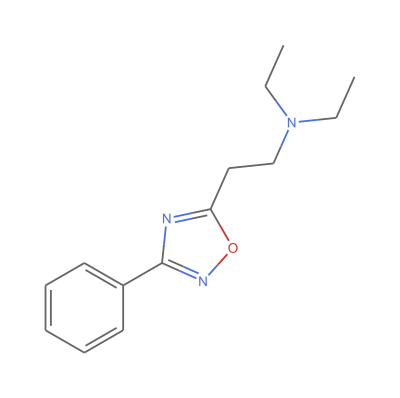

```mathematica
MoleculePlot[MoleculeModify[Molecule[xyzfile],"AddHydrogens"]]
```

```mathematica
sdffile=Molecule[…]
```

Molecule::valenc: Invalid valence for nitrogen atom at position 9.

Molecule[…]

Molecule::valenc: Invalid valence for nitrogen atom at position 9.

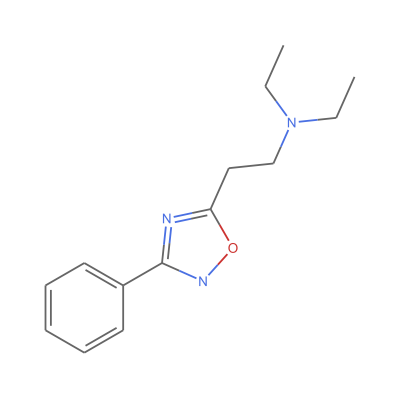

-Graphics-

```mathematica
MoleculePlot[MoleculeModify[Molecule[sdffile],"AddHydrogens"]]
```

Above, the .xyz geometry which had been exported from Mathematica had a valid bonding structure, but the .sdf conversion of that geometry had an invalid valence at the second ring nitrogen. Therefore, this is likely a bug in Open Babel, the program used to convert .xyz geometries into .sdf format.

Let’s try exporting from Mathematica as an SDF rather than using Babel to convert.

This line of code exports the .sdf format 3D geometry of Compound 2338 after generating it from the SMILES string from DrugBank.

Export[StringJoin["<directory>"], MoleculeModify[Molecule["CCN(CC)CCc1nc(-c2ccccc2)no1"], "AddHydrogens"]]

#### Compound 2382: Mathematica XYZ exporting issue

Here is the .xyz geometry exported from Mathematica:

```mathematica
xyz2382=Molecule[…]
```

Molecule[…]

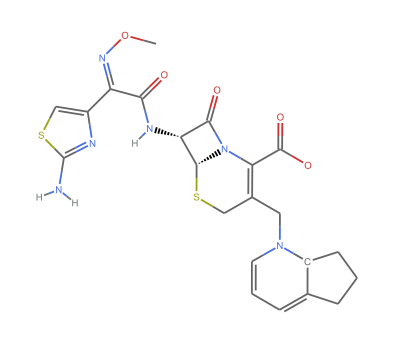

```mathematica
MoleculePlot[MoleculeModify[Molecule[xyz2382],"AddHydrogens"]]
```

Here’s the version created by converting the above to an sdf format geometry:

```mathematica
sdf2382=Molecule[…]
```

Molecule[…]

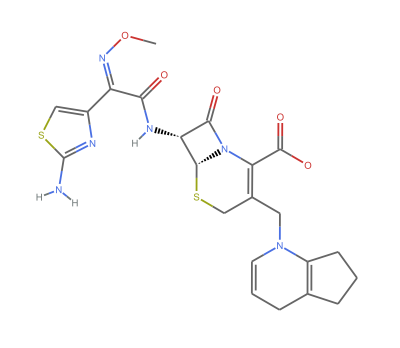

```mathematica
MoleculePlot[MoleculeModify[Molecule[sdf2382],"AddHydrogens"]]
```

It turned out that both the above geometries were incorrect, which makes this case different from Compound 2338 above. Here’s the actual structure:

-Graphics-

Further, Mathematica can interpret the SMILES string I was given for this molecule, as shown by the molecule plot below:

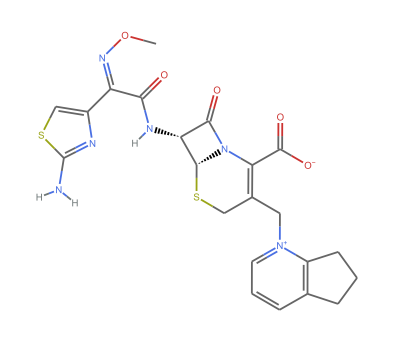

```mathematica
MoleculePlot[MoleculeModify[Molecule["CO/N=C(\\C(N[C@@H]([C@H]1SCC(C[n+]2c(CCC3)c3ccc2)=C(C([O-])=O)N11)C1=O)=O)/c1csc(N)n1"],"AddHydrogens"]]
```

I went on to confirm that when this SMILES string was used to create a .xyz file for export, the charge information was lost, using:

Export[StringJoin[“<directory>”<>”.xyz”],MoleculeModify[Molecule[“CO/N=C(\\C(N[C@@H]([C@H]1SCC(C[n+]2c(CCC3)c3ccc2)=C(C([O-])=O)N11)C1=O)=O)/c1csc(N)n1”],”AddHydrogens”]]

When that geometry was re-imported and plotted we got the following:

```mathematica
xyz2382reimported=Molecule[…]
```

Molecule[…]

```mathematica
MoleculePlot[MoleculeModify[Molecule[xyz2382reimported],"AddHydrogens"]]
```

-Graphics-

Confirmed - molecule exported to XYZ lost charge information.

For this problem, the solution is the same as Compound 2338: Export the molecule in .sdf format to begin with. Hindsight is 20/20.

Export[StringJoin[“<directory>”<>”.sdf”],MoleculeModify[Molecule[“CO/N=C(\\C(N[C@@H]([C@H]1SCC(C[n+]2c(CCC3)c3ccc2)=C(C([O-])=O)N11)C1=O)=O)/c1csc(N)n1”],”AddHydrogens”]]

```mathematica
fixedCompound2382=Molecule[…]
```

Molecule[…]

```mathematica
MoleculePlot[MoleculeModify[Molecule[fixedCompound2382],"AddHydrogens"]]
```

-Graphics-

Correct geometry. Problem solved!

In the XYZ export, Mathematica failed to specify the Nitrogen charge. I think getting it right would follow the convention here: https://wiki.jmol.org/index.php/File_formats/Formats/XYZ

#### Compound 2207, Tucatinib: MOPOUT to SDF file conversion may create geometry errors in special cases

This compound has the final unique type of issue in my workflow that I discovered. Let’s follow one final round of detective work:

Mathematica interpretation of the SMILES string in the library: OK.

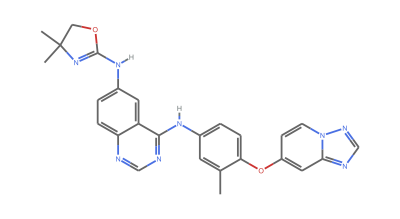

```mathematica
MoleculePlot[Molecule["CC1=CC(NC2=NC=NC3=CC=C(NC4=NC(C)(C)CO4)C=C23)=CC=C1OC1=CC2=NC=NN2C=C1"]]
```

Structure generated by Mathematica and used in my subsequent calculations: OK

```mathematica
usedincalcs2207=Molecule[…]
```

Molecule[…]

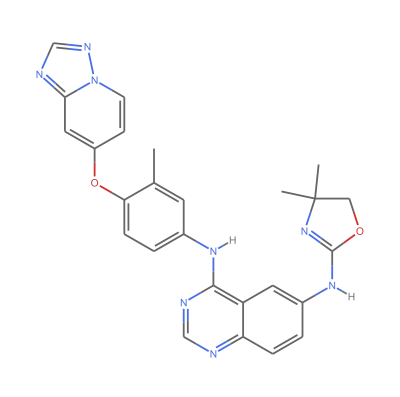

```mathematica
MoleculePlot[usedincalcs2207]
```

Structure interpreted from MOPAC output file: messed up

```mathematica
mopOutConverted=Molecule[…]
```

Molecule[…]

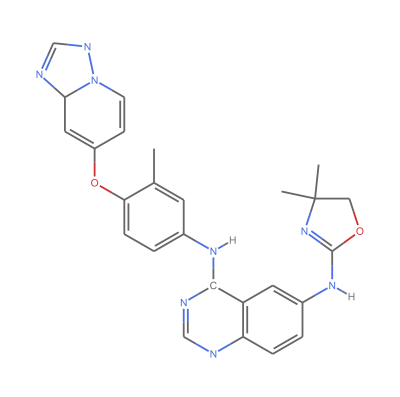

```mathematica
MoleculePlot[mopOutConverted]
```

There’s a serious valence error in the structure above. Hilariously, though, the geometry in the actual MOPAC output file is probably correct, since we have verified that the input geometry was correct and no errors were thrown. Thus, the atom positions in the perturbed .sdf structure above should also be correct. These static conformers can potentially still be used in in silico screening, but it would be better to fix the error!

This problem could be solved by building a MOPAC output file interpreter into Mathematica. This interpreter just has to be more robust than Open Babel’s at extracting geometries.  Conjugated π systems like that of tucatinib are thought to be the culprits for some molecular geometry interpretation issues.

### VI. Extract final conformers, visualize

Optimized geometries generated at the end of MOPAC optimization runs were extracted from the MOPAC output files and converted to XYZ and SDF formats using Open Babel again. 

Some examples of molecules journeying through this multi-stage process are displayed graphically at the top of this report.

## References

1	I. Y. Kanal, J. A. Keith, G. R. Hutchison, A sobering assessment of small-molecule force field methods for low energy conformer predictions. International Journal of Quantum Chemistry 118 (2017).

2	N M O'Boyle, M Banck, C A James, C Morley, T Vandermeersch, and G R Hutchison. "Open Babel: An open chemical toolbox." J. Cheminf. (2011), 3, 33. DOI:10.1186/1758-2946-3-33

3	MOPAC2016, James J. P. Stewart, Stewart Computational Chemistry, Colorado Springs, CO, USA, HTTP://OpenMOPAC.net (2016)

4	Wishart DS, Feunang YD, Guo AC, Lo EJ, Marcu A, Grant JR, Sajed T, Johnson D, Li C, Sayeeda Z, Assempour N, Iynkkaran I, Liu Y, Maciejewski A, Gale N, Wilson A, Chin L, Cummings R, Le D, Pon A, Knox C, Wilson M. DrugBank 5.0: a major update to the DrugBank database for 2018. Nucleic Acids Res. 2017 Nov 8. doi: 10.1093/nar/gkx1037.